# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll102`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"final"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
ImageData[idd];
```

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={(*{100,100},*){2,2}(*,{200,200},{500,300}*)};
ims=Table[
nx=dims[[1]]/r;
ny=dims[[2]]/r;

tim=4;
{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+44*tim},{nx,nx+103*tim}]&/@{ia,ib,id,io}

(*
im=ImageData[iaa];
imdis=ImageData[idd];
pos=Flatten[Table[{x-imdis[[y,x]],ImageDimensions[iaa][[2]]+1-y}->im[[y,x]],{y,1,ImageDimensions[iaa][[2]]},{x,1,ImageDimensions[iaa][[1]]}]];

SetSystemOptions["MaxPatternMatchRecursion"->Infinity];
iaaa=ReplacePixelValue[iaa,pos[[1;;-1]]];
*)

,{dims,listDims}]

max=MinMax[Flatten[ImageData[idd]*0.1]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

max dv=3.86009

{413,177}

```mathematica
(*ListAnimate[{iaa,iaaa}];*)
ListAnimate[{iaa,ibb}];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],im[[3]],minmax[[2]],minmax,Range[1,1+103*tim,steps],Range[1,1+44*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,1+44*tim-y]&/@realPVTable[[y]],{y,1,1+44*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## More in depth

```mathematica
ImageDimensions[idd]
```

{413,177}

```mathematica
lvl=5;
```

```mathematica
k=1;
{ka,kd}=ImageData[#][[k]]&/@{iaa,idd};
pyra=pyrFuncGen[ka,lvl];

kb=Table[pyra[[1,1]][x+kd[[x]]*0.1],{x,1,1+102*tim}];

pyrb=pyrFuncGen[kb,lvl];


pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10*0.1,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10*0.1,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
lt=lineTest[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedCorrelation"];
```

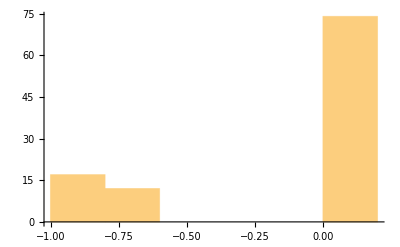

```mathematica
Histogram[Total[#]&/@lt[[All,1;;2]]]
```

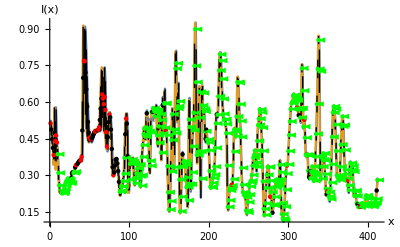

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

```mathematica
(*pixelIterGraphics[10,1,0,20,{{0.,0.}},condition,5, 1,pyrab[[1;;1]],e,"ConstrainedCorrelation"]*)
```

## Big Tests

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
testLevels={{1,5}};
e=0.0001;
n=1;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10*0.1,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10*0.1,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
levelTable=Table[

bigTest[steps,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[levelTable]]
```

levelTable Dimensions={1,1,1,4}

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

solution=ImageData[-ims[[which,3]]*0.1];
levelTable[[1,which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[levelTable[[1,which,1,1,All,All,1]]]]])/((1+103.*tim)*(1+44.*tim));

vals=Table[
ps=Select[levelTable[[1,which,1,1,y,All,All]],1<Round[#[[1]]]<(1+103.*tim)&];
(ps[[All,2]]-solution[[y,Round[ps[[All,1]]]]])^2

,{y,Length[levelTable[[1,which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,0.204205,Density= ,0.310379}}

### Images

```mathematica
imagesTable=Table[

solution=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]]*0.1,scale,{0,1}]]}]];

images=ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{ims[[which,1;;2]],levelTable[[1,which,1,4]],solution}],{4000}];

Grid[{images,numbersTable[[which]]}]

,{which,Length[ims]}];
```

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->150];
```

```mathematica
imFinal=Legended[Grid[Flatten[{imagesTable},{{2},{1}}]],legendBar]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 0.204205 | Density=  | 0.310379

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->100]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\sintel102-bamboo-final-im.pdf